### useful function

```mathematica
Load observable[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
Plot mag[type_,D_,χ_,range_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\D",#3,"_χ",#4,"_observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,range[[1]],range[[2]],range[[3]]}];
data=Load observable/@files;
x=Table[i,{i,range[[1]],range[[2]],range[[3]]}];
ListPlot[Table[Table[{x[[i]],data[[i]][[j]]},{i,1,Length[data]}],{j,1,5}],PlotLegends->{mag,ferro,stripy,zigzag,Neel,etol,ΔE,Cross},Joined->Table[True,{i,1,Length[data]}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
Plot ΔE[type_,D_,χ_,range_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\D",#3,"_χ",#4,"_observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,range[[1]],range[[2]],range[[3]]}];
data=Load observable/@files;
x=Table[i,{i,range[[1]],range[[2]],range[[3]]}];
ListPlot[Table[{x[[i]],data[[i]][[7]]},{i,1,Length[data]}],PlotLegends->ΔE,Joined->Table[True,{i,1,Length[data]}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
```

## out of plane

### D=2

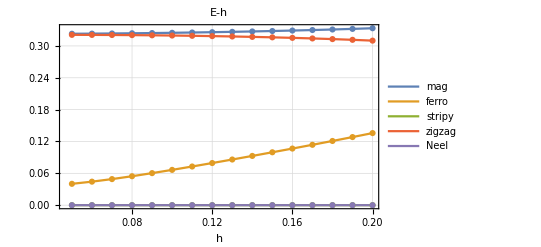

```mathematica
Plot mag[zigzag,2,20]
```

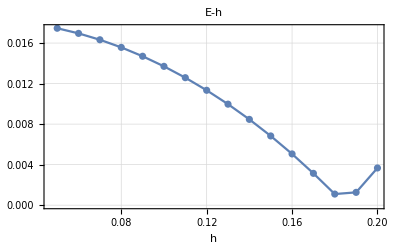

```mathematica
Plot ΔE[zigzag,2,20]
```

### D=4

```mathematica
Load observable[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
Plot mag[type_,D_,χ_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type]]],{i,0.05,0.20,0.01}];
data=Load observable/@files;
ListPlot[Table[Table[{(i+4)/100,data[[i]][[j]]},{i,1,16}],{j,1,5}],PlotLegends->{mag,ferro,stripy,zigzag,Neel,etol,ΔE,Cross},Joined->Table[True,{i,1,6}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
Plot ΔE[type_,D_,χ_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,0.05,0.20,0.01}];
data=Load observable/@files;
ListPlot[Table[{(i+4)/100,data zigzag[[i]][[7]]},{i,1,16}],PlotLegends->ΔE,Joined->Table[True,{i,1,5}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
```

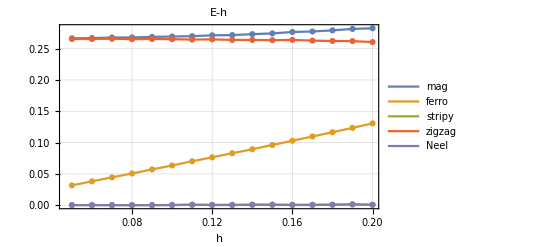

```mathematica
Plot mag[zigzag,4,80]
```

```mathematica
Plot mag[ferro,4,80]
```

OpenRead::noopen: 无法打开 E:\1 - research\4.9 - AutoDiff\data\ADBCVUMPS\K_J_Γ_Γ′_1x2\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_0.05_ferro\observable.log.

StringSplit::strse: StringSplit[$Failed] 的位置 1 处应该是字符串或者由字符串组成的列表.

StringReplace::strse: StringReplace[StringSplit[$Failed],e→*10^] 的位置 1 处应该是字符串或者由字符串组成的列表.

ToExpression::notstrbox: StringReplace[StringSplit[$Failed],e→*10^] 不是一个字符串或者框符. ToExpression 只能将字符串或者框符解释为 Wolfram 语言输入.

OpenRead::noopen: 无法打开 E:\1 - research\4.9 - AutoDiff\data\ADBCVUMPS\K_J_Γ_Γ′_1x2\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_0.06_ferro\observable.log.

StringSplit::strse: StringSplit[$Failed] 的位置 1 处应该是字符串或者由字符串组成的列表.

StringReplace::strse: StringReplace[StringSplit[$Failed],e→*10^] 的位置 1 处应该是字符串或者由字符串组成的列表.

ToExpression::notstrbox: StringReplace[StringSplit[$Failed],e→*10^] 不是一个字符串或者框符. ToExpression 只能将字符串或者框符解释为 Wolfram 语言输入.

OpenRead::noopen: 无法打开 E:\1 - research\4.9 - AutoDiff\data\ADBCVUMPS\K_J_Γ_Γ′_1x2\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_0.07_ferro\observable.log.

General::stop: 在本次计算中，OpenRead::noopen 的进一步输出将被抑制.

StringSplit::strse: StringSplit[$Failed] 的位置 1 处应该是字符串或者由字符串组成的列表.

General::stop: 在本次计算中，StringSplit::strse 的进一步输出将被抑制.

StringReplace::strse: StringReplace[StringSplit[$Failed],e→*10^] 的位置 1 处应该是字符串或者由字符串组成的列表.

General::stop: 在本次计算中，StringReplace::strse 的进一步输出将被抑制.

ToExpression::notstrbox: StringReplace[StringSplit[$Failed],e→*10^] 不是一个字符串或者框符. ToExpression 只能将字符串或者框符解释为 Wolfram 语言输入.

General::stop: 在本次计算中，ToExpression::notstrbox 的进一步输出将被抑制.

Part::partd: 部分指定 $Failed⟦1⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

-Graphics-

### D=5

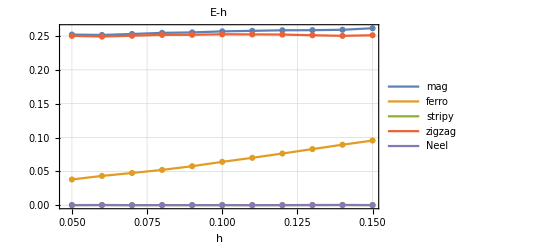

```mathematica
Plot mag[zigzag,5,100,{0.05,0.15,0.01}]
```

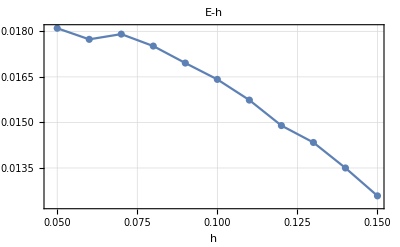

```mathematica
Plot ΔE[zigzag,5,100,{0.05,0.15,0.01}]
```

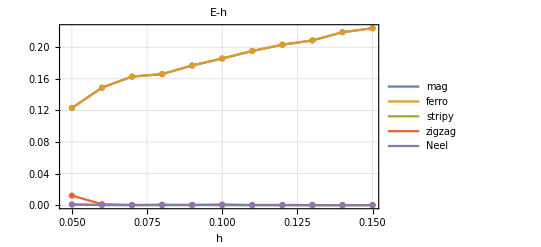

```mathematica
Plot mag[ferro,5,100,{0.05,0.15,0.01}]
```

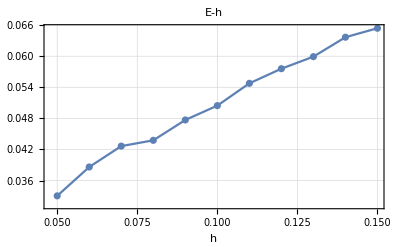

```mathematica
Plot ΔE[ferro,5,100,{0.05,0.15,0.01}]
```

## in plane

### D=4

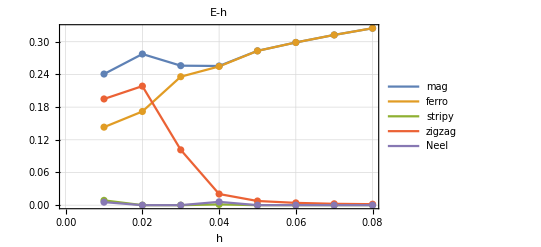

```mathematica
Plot mag[random,4,80,{0.01,0.08,0.01}]
```

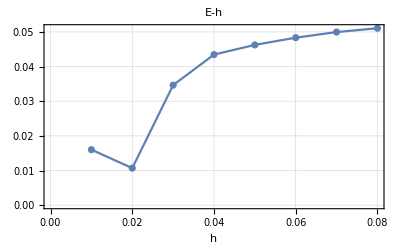

```mathematica
Plot ΔE[random,4,80,{0.01,0.08,0.01}]
```

### D=5

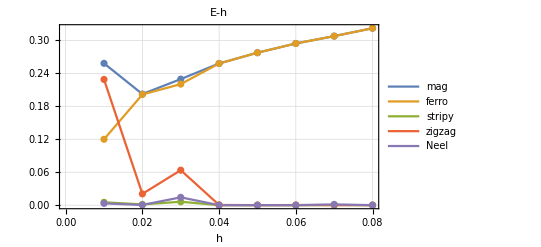

```mathematica
Plot mag[random,5,100,{0.01,0.08,0.01}]
```

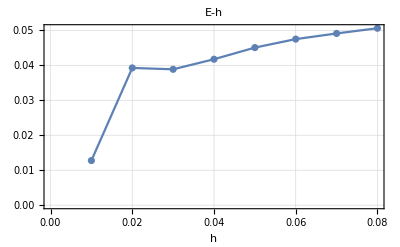

```mathematica
Plot ΔE[random,5,100,{0.01,0.08,0.01}]
```